```mathematica
(* Metric *)
gcov=DiagonalMatrix[{-(1-2/r),r/(r-2),r^2,r^2 Sin[theta]^2}];
gcon=FullSimplify[Inverse[gcov]];
MatrixForm[gcov]
MatrixForm[gcon]

FullSimplify[Det[gcov]]

(* Boosts vector au from the frame moving at velocity wu to frame moving at velocity uu *)
LorentzBoostUpper[au_,uu_,ud_,wu_,wd_]:=Block[{lorentzgam,Omeg,OmegSq,Lam},lorentzgam=-wu.ud;Omeg=Table[uu[[mu]]wd[[nu]]-wu[[mu]]ud[[nu]],{mu,1,4},{nu,1,4}]//.consts;OmegSq=Table[Sum[Omeg[[mu,sigma]]Omeg[[sigma,nu]],{sigma,1,4}],{mu,1,4},{nu,1,4}];Lam=IdentityMatrix[4]+OmegSq/(lorentzgam+1)+Omeg;Lam.au];
InverseLorentzBoostUpper[au_,uu_,ud_,wu_,wd_]:=Block[{neguu,negud},neguu=-uu; neguu[[1]]=-neguu[[1]];negud=-ud; negud[[1]]=-negud[[1]];LorentzBoostUpper[au,neguu,negud,wu,wd]];

InverseLorentzBoostLower[ad_,uu_,ud_,wu_,wd_]:=Block[{neguu,negud},neguu=-uu; neguu[[1]]=-neguu[[1]];negud=-ud; negud[[1]]=-negud[[1]];LorentzBoostLower[ad,neguu,negud,wu,wd]];

LorentzBoostLower[ad_,uu_,ud_,wu_,wd_]:=LorentzBoostUpper[ad,ud,uu,wd,wu];

vel3p2vel3u[vel3phys_]:={1,Sqrt[gcon[[2,2]]]Sqrt[-gcov[[1,1]]] vel3phys[[2]],Sqrt[gcon[[3,3]]] Sqrt[-gcov[[1,1]]]vel3phys[[3]],Sqrt[gcon[[4,4]]]Sqrt[-gcov[[1,1]]] vel3phys[[4]]};

vel3u2vel4u[vel3u_]:=Block[{uut},uut=1/(-gcov[[1,1]]-Sum[gcov[[i,i]] vel3u[[i]]^2,{i,2,4}])^(1/2); vel3u uut];

vel3p2vel4u[vel3phys_]:=vel3u2vel4u[vel3p2vel3u[vel3phys]];
```

(-1+2/r | 0 | 0 | 0
0 | r/(-2+r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[theta]^2)

(r/(2-r) | 0 | 0 | 0
0 | (-2+r)/r | 0 | 0
0 | 0 | 1/r^2 | 0
0 | 0 | 0 | Csc[theta]^2/r^2)

-r^4 Sin[theta]^2

```mathematica
(* Rotating boost *)
(* define rotation in terms of fluid quantities *)
vu3hat = uu[[4]]/uu[[1]]*Sqrt[-gcov[[4,4]]/gcov[[1,1]]];
Omega=vu3hat/Sqrt[-gcov[[4,4]]/gcov[[1,1]]]
gamma=-(gcov[[1,1]]+gcov[[1,4]]*Omega)/Sqrt[gcov[[1,1]]*(gcov[[1,1]]+2*gcov[[1,4]]*Omega+gcov[[4,4]]*Omega^2)]
Lambda={{gamma*(1-gcov[[1,4]]*Omega/(gcov[[1,1]]+gcov[[1,4]]*Omega)),0,0,gamma*gcov[[4,4]]*Omega/(gcov[[1,1]]+gcov[[1,4]]*Omega)},{0,1,0,0},{0,0,1,0},{-gamma*gcov[[1,1]]*Omega/(gcov[[1,1]]+gcov[[1,4]]*Omega),0,0,gamma(1+gcov[[1,4]]*Omega/(gcov[[1,1]]+gcov[[1,4]]*Omega))}}
MatrixForm[Lambda]

FullSimplify[Det[Lambda]]
```

0.1013592182869906266995667266

(1-2/r)/(√((-1+2/r) (-1+2/r+0.0102736911317498150735596285 r^2 Sin[theta]^2)))

{{(1-2/r)/(√((-1+2/r) (-1+2/r+0.0102736911317498150735596285 r^2 Sin[theta]^2))),0,0,(0.1013592182869906266995667266 (1-2/r) r^2 Sin[theta]^2)/((-1+2/r) √((-1+2/r) (-1+2/r+0.0102736911317498150735596285 r^2 Sin[theta]^2)))},{0,1,0,0},{0,0,1,0},{-(0.1013592182869906266995667266 (1-2/r))/(√((-1+2/r) (-1+2/r+0.0102736911317498150735596285 r^2 Sin[theta]^2))),0,0,(1-2/r)/(√((-1+2/r) (-1+2/r+0.0102736911317498150735596285 r^2 Sin[theta]^2)))}}

((1-2/r)/(√((-1+2/r) (-1+2/r+0.0102736911317498150735596285 r^2 Sin[theta]^2))) | 0 | 0 | (0.1013592182869906266995667266 (1-2/r) r^2 Sin[theta]^2)/((-1+2/r) √((-1+2/r) (-1+2/r+0.0102736911317498150735596285 r^2 Sin[theta]^2)))
0 | 1 | 0 | 0
0 | 0 | 1 | 0
-(0.1013592182869906266995667266 (1-2/r))/(√((-1+2/r) (-1+2/r+0.0102736911317498150735596285 r^2 Sin[theta]^2))) | 0 | 0 | (1-2/r)/(√((-1+2/r) (-1+2/r+0.0102736911317498150735596285 r^2 Sin[theta]^2))))

1.

```mathematica
(* Setup fluid equations *)
Clear[ut,vp]
consts={gam->4/3,u->0.5``30,rho->0.1``30,r->4.6``30,theta->Pi/2,phi->0.0``30}
(*uu=ut{1,-0.1,0,  1/r^(3/2)}/.consts*) (* Kepler motion in phi, small radial velocity in r *)
(*uu={ut,-0.0,0, 0/r^(3/2)}/.consts*) (* Kepler motion in phi, small radial velocity in r *)
(*uu=ut{1,0.57``30,1.0``30*10^(-30),1/r^(3/2)}//.consts*) (* kinda tough for mathematica *)
uu=ut{1,-0.38395``30,1.0``30*10^(-30),1/r^(3/2)}//.consts
ud=Table[Sum[gcov[[ii,jj]]*uu[[ii]],{ii,1,4}],{jj,1,4}]//.consts
sol=Solve[Sum[uu[[ii]]ud[[ii]],{ii,1,4}]==-1,ut];
ut=ut/.sol[[2]]

v3u={uu[[1]]/uu[[1]],uu[[2]]/uu[[1]],uu[[3]]/uu[[1]],uu[[4]]/uu[[1]]};
v3uortho=Table[v3u[[i]]*Sqrt[If[i==1,1,-1]*gcov[[i,i]]/gcov[[1,1]]],{i,1,4}]//.consts;

(* boost fluid velocity into rotating frame *)
uurot=Table[Sum[uu[[i]]*Lambda[[j,i]],{i,1,4}],{j,1,4}]//.consts;
v3urot={uurot[[1]]/uurot[[1]],uurot[[2]]/uurot[[1]],uurot[[3]]/uurot[[1]],uurot[[4]]/uurot[[1]]};
v3urotortho=Table[v3urot[[i]]*Sqrt[If[i==1,1,-1]*gcov[[i,i]]/gcov[[1,1]]],{i,1,4}]//.consts;


wu={1/Sqrt[-gcov[[1,1]]] ,0,0,0}//.consts;
wd=Table[Sum[gcov[[ii,jj]]*wu[[ii]],{ii,1,4}],{jj,1,4}]//.consts;
lorentzgam=-wu.ud//.consts;

bsq0=10*(gam-1)*u//.consts
bflu={0,-0.00703939177500395``30,6.04549046091683``30*10^(-06),0.00687905349136715``30}
(*bflu={0,-0.001,0,-0.006}*)
(*bflu={0,-0.001,10^(-06),-0.001}*)
bfld=Table[Sum[gcov[[ii,jj]]*bflu[[ii]],{ii,1,4}],{jj,1,4}]//.consts
bflsq=Sum[bflu[[ii]]*bfld[[ii]],{ii,1,4}]
bflu=bflu*Sqrt[bsq0/bflsq]
bfld=bfld*Sqrt[bsq0/bflsq]
bflsqnew=Sum[bflu[[ii]]*bfld[[ii]],{ii,1,4}]


(* Boost back into Lab frame *)
bu=InverseLorentzBoostUpper[bflu,uu,ud,wu,wd]
bd=InverseLorentzBoostLower[bfld,uu,ud,wu,wd];

p=(gam-1)*u//.consts
WW=rho+u+p//.consts
bsq=Sum[bu[[i]]*bu[[j]]*gcov[[i,j]],{i,1,4},{j,1,4}]//.consts
EF=(bsq+WW)//.consts
cs2=gam*p/WW//.consts
va2=bsq/EF//.consts
cms2=(va2+cs2*(1-va2))

(* Boost bu to the fluid frame *)
bflu1=LorentzBoostUpper[bu,uu,ud,wu,wd]
bflu
bfld1=LorentzBoostLower[bd,uu,ud,wu,wd]
bfld
bu.bd
bflu.bfld
bflu1.bfld1
```

{gam→4/3,u→0.5,rho→0.1,r→4.6,theta→π/2,phi→0.}

{ut,-0.38395 ut,1.×10^-30 ut,0.10135921828699062669956672658 ut}

{-0.565217391304347826086956521739 ut,-0.67929615384615384615384615385 ut,2.116×10^-29 ut,2.14476105895272166096283193443 ut}

3.390116285852356882946007545

1.6666666666666666666666666667

{0,-0.00703939177500395,6.04549046091683×10^-6,0.00687905349136715}

{0,-0.0124543085250069884615384615,0.0001279225781530001228,0.145560771877328894}

0.00108899186633785832018289788

{0,-0.275389383100466884137833281,0.00023650678095277753111339424,0.269116758642354342306364057}

{0,-0.487227370100826025782320419,0.00500448348496077255835942212,5.69451061287221788320266344}

1.66666666666666666666666667

{3.44626886589388242713888087,-1.22571904579350552268197848,0.000236506780952777531113394242,0.51999492435535310754684389}

0.16666666666666666666666666667

0.76666666666666666666666666667

1.6666666666666666666666667

2.4333333333333333333333333

0.28985507246376811594202898551

0.6849315068493150684931507

0.7762557077625570776255708

{0.,-0.2753893831004668841378333,0.00023650678095277753111339424,0.26911675864235434230636406}

{0,-0.275389383100466884137833281,0.00023650678095277753111339424,0.269116758642354342306364057}

{0.,-0.4872273701008260257823204,0.00500448348496077255835942212,5.6945106128722178832026634}

{0,-0.487227370100826025782320419,0.00500448348496077255835942212,5.69451061287221788320266344}

1.6666666666666666666666667

1.66666666666666666666666667

1.6666666666666666666666667

```mathematica
(* check ut, fluid 3-velocity, and fluid 3-velocity in rotating frame  *)
ut
v3uortho
v3urotortho
```

3.390116285852356882946007545

{1.,-0.6792961538461538461538461538,6.118571980202821551429700309×10^-30,0.6201736729460422809512779408}

{1.,-0.865936085992516229158745055,7.79967948059405835992423978×10^-30,0.}

```mathematica
(* pick one single dispersion relation *)
(*eq1=0==(1/k1^2*(-wfl^2+cs2*ksq));*)
(*eq1=0==(1/k1^2*(-wfl^2+kdotva2));*)
(*eq1=0==(1/k1^2*(-wfl^2+(va2+cs2*(1-va2))*ksq));*)
(* Note Disp stored symbolically, but once variables set to something else the sub-symbols are only intrepreted, not the ones replaced *)
Clear[Disp];
Disp[wfl_,ksq_,cms2_,cs2_,kdotva2_]:=(wfl^4-wfl^2*(ksq*cms2+cs2*kdotva2)+ksq*cs2*kdotva2);
(*Disp[wfl_,ksq_,cms2_,cs2_,kdotva2_]:=(wfl^2*(wfl^2-cms2*ksq));*)
```

```mathematica
(* Solve for HARM phase speed *)
(*Clear[bsq,va2,cs2,bu,bd,ku,kd,Kd,Ku,uu,ud,EF,WW,p,cm2]*)
(* Setup wave *)
kd=k*{-vphase Sqrt[-gcov[[1,1]]],Cos[alpha] Sqrt[gcov[[2,2]]],0,Sin[alpha] Sqrt[gcov[[4,4]]]}/.consts
ku=Table[Sum[gcon[[ii,jj]]*kd[[ii]],{ii,1,4}],{jj,1,4}]//.consts
wfl=-(kd.uu)//.consts
ksq=(kd.ku+wfl^2)//.consts
kdotva=kd.bu/Sqrt[EF]//.consts
kdotva2=kdotva^2
FullSimplify[Sum[bu[[i]]*uu[[j]]*gcov[[i,j]],{i,1,4},{j,1,4}]]//.consts

(* fast/slow modes *)
eq1x=0==(1/k^4*(Disp[wfl,ksq,cms2,cs2,kdotva2]));
eq1x=Rationalize[eq1x]

Clear[vphase]
sols1x=Solve[eq1x,vphase];
vp=sols1x[[4,1,2]]//.consts;
vm=sols1x[[1,1,2]]//.consts;
vrp=vp Cos[alpha]//.consts;
vrm=vm Cos[alpha]//.consts;
v1m=vm Cos[alpha]//.consts//.alpha->0
v1p=vp Cos[alpha]//.consts//.alpha->0
v3m=vm Sin[alpha]//.consts//.alpha->Pi/2
v3p=vp Sin[alpha]//.consts//.alpha->Pi/2

v3p
v3m
Print["v1p"];
v1p
v1m
```

{-0.7518094115561122889280350095553 k vphase,1.33012434352235251118036963229 k Cos[alpha],0,4.6 k Sin[alpha]}

{1.33012434352235251118036963229 k vphase,0.751809411556112288928035009555 k Cos[alpha],0,0.21739130434782608695652173913 k Sin[alpha]}

2.548721329973453388586996694 k vphase+1.731336596676620835123344596 k Cos[alpha]-1.580649868525558391038101193 k Sin[alpha]

-1. k^2 vphase^2+1. k^2 Cos[alpha]^2+1. k^2 Sin[alpha]^2+(2.548721329973453388586996694 k vphase+1.731336596676620835123344596 k Cos[alpha]-1.580649868525558391038101193 k Sin[alpha])^2

0.64106076475603234432571317 (-2.59093736813183020332420272 k vphase-1.63035874112893086859608232 k Cos[alpha]+2.3919766520346242947154819 k Sin[alpha])

0.41095890410958904109589041 (-2.59093736813183020332420272 k vphase-1.63035874112893086859608232 k Cos[alpha]+2.3919766520346242947154819 k Sin[alpha])^2

0.

0==1/k^4(2.548721329973453388586996694 k vphase+1.731336596676620835123344596 k Cos[alpha]-1.580649868525558391038101193 k Sin[alpha])^2 ((2.548721329973453388586996694 k vphase+1.731336596676620835123344596 k Cos[alpha]-1.580649868525558391038101193 k Sin[alpha])^2-170/219 (-k^2 vphase^2+k^2 Cos[alpha]^2+k^2 Sin[alpha]^2+(2.548721329973453388586996694 k vphase+1.731336596676620835123344596 k Cos[alpha]-1.580649868525558391038101193 k Sin[alpha])^2))

-0.6792961538461538461538462

0.0505778037247820425527772

0.6201736729460422809512779

0.915008087279310366026142

0.915008087279310366026142

0.6201736729460422809512779

v1p

0.0505778037247820425527772

-0.6792961538461538461538462

{{vphase→-0.924202767767433211+0. ⅈ},{vphase→-0.71252654440389732+0. ⅈ},{vphase→-0.665040565081906875+0. ⅈ},{vphase→-0.000026302864779972+0. ⅈ}}

{{vphase→-0.924202767767433211},{vphase→-0.71252654440389732},{vphase→-0.665040565081906875},{vphase→-0.000026302864779972}}

{{vphase→0.039262015687045423},{vphase→0.399067255974327673},{vphase→0.707374479272454122},{vphase→0.915001269200972393}}

{{-0.000026302864779972,0},{-0.924202767767433211,0}}

{{0,0.915001269200972393},{0,0.039262015687045423}}

{{vphase→-0.924202767767433211+0. ⅈ},{vphase→-0.71252654440389732+0. ⅈ},{vphase→-0.665040565081906875+0. ⅈ},{vphase→-0.000026302864779972+0. ⅈ}}

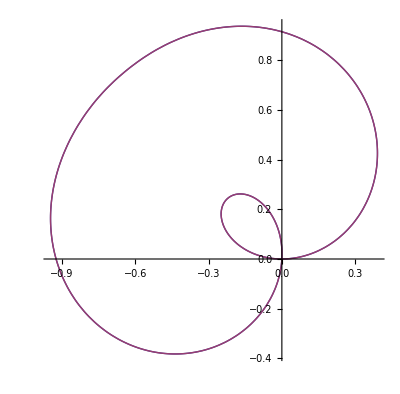

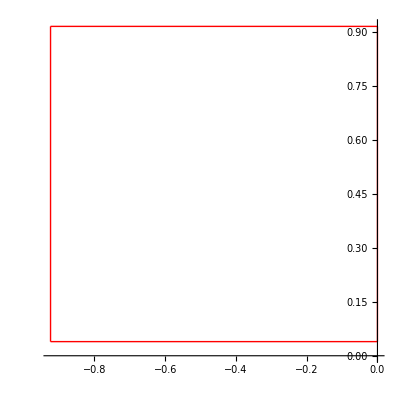

{alpha→{-0.630162-1.03612×10^-15 ⅈ,0.827672+1.55806×10^-18 ⅈ}}

{alpha→{-1.5708+3.24589×10^-27 ⅈ,1.5708+1.64298×10^-34 ⅈ}}

1.5708+1.64298×10^-34 ⅈ

```mathematica
sols1x//.consts//.alpha->0
Chop[sols1x//.consts//.alpha->0]
Chop[sols1x//.consts//.alpha->Pi/2]
Chop[{{vp Cos[alpha],vp Sin[alpha]},{vm Cos[alpha],vm Sin[alpha]}}/.alpha->0]
Chop[{{vp Cos[alpha],vp Sin[alpha]},{vm Cos[alpha],vm Sin[alpha]}}/.alpha->Pi/2]

Sort[sols1x//.consts//.alpha->0]
(*Plot[{vm,vp},{alpha,-Pi,Pi}]*)

plboostk=ParametricPlot[{{vp Cos[alpha],vp Sin[alpha]},{vm Cos[alpha],vm Sin[alpha]}},{alpha,0,2*Pi}]

plotvpm=ParametricPlot[{{v1m,v3m+(v3p-v3m)t},{v1p,v3m+(v3p-v3m)t},{v1m+(v1p-v1m)t,v3m},{v1m+(v1p-v1m)t,v3p}},{t,0,1},PlotStyle->{RGBColor[1,0,0]}]

alphamaxes=FindRoot[D[vp Cos[alpha],alpha]==0,{alpha,{-1,1}}]
alphamaxes=FindRoot[vp Cos[alpha]==0,{alpha,{-1,1}}]
alphamaxes[[1,2,2]]
```

```mathematica
(* Comoving wave vector *)
kfld=kfl*{-vphase Sqrt[-gcov[[1,1]]],Cos[alpha] Sqrt[gcov[[2,2]]],0,Sin[alpha] Sqrt[gcov[[4,4]]]}/.consts;
kflu=Table[Sum[gcon[[ii,jj]]*kfld[[ii]],{ii,1,4}],{jj,1,4}]//.consts;

(* Boost uu to the fluid frame *)
uflu= LorentzBoostUpper[uu,uu,ud,wu,wd];
ufld=LorentzBoostLower[ud,uu,ud,wu,wd];

(* Boost bu to the fluid frame *)
bflu=LorentzBoostUpper[bu,uu,ud,wu,wd];
bfld=LorentzBoostLower[bd,uu,ud,wu,wd];

wfl=-(kfld.uflu)//.consts
ksq=(kfld.kflu+wfl^2)//.consts
kdotva=kfld.bflu/Sqrt[EF]//.consts
kdotva2=kdotva^2

(* fast/slow modes *)
eq1x=0==(1/kfl^4*(Disp[wfl,ksq,cms2,cs2,kdotva2]));
eq1x=Rationalize[eq1x];
```

1. kfl vphase+0. kfl Cos[alpha]+0. kfl Sin[alpha]

-1. kfl^2 vphase^2+1. kfl^2 Cos[alpha]^2+1. kfl^2 Sin[alpha]^2+(1. kfl vphase+0. kfl Cos[alpha]+0. kfl Sin[alpha])^2

0.64106076475603234432571317 (0. kfl vphase-0.3663021224095341530720343 kfl Cos[alpha]+1.2379370897548299746092747 kfl Sin[alpha])

0.41095890410958904109589041 (0. kfl vphase-0.3663021224095341530720343 kfl Cos[alpha]+1.2379370897548299746092747 kfl Sin[alpha])^2

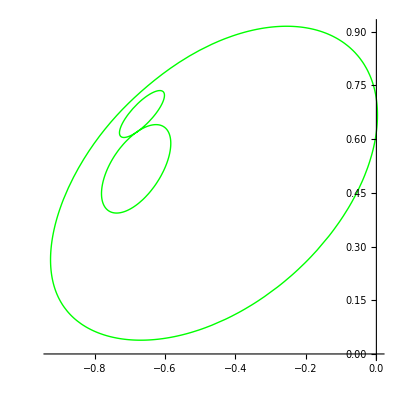

```mathematica
(* Create comoving wave 4-vel from wfl/kphys *)
Clear[vphase]
sols1x=Solve[eq1x,vphase];
absvp=sols1x[[4,1,2]];
absvm=sols1x[[1,1,2]];
vpphys={ 1, absvp Cos[alpha],0,absvp Sin[alpha]}//.consts;
vmphys={ 1, absvm Cos[alpha],0,absvm Sin[alpha]}//.consts;
upu=vel3p2vel4u[vpphys];
upd=Table[Sum[gcov[[ii,jj]]*upu[[ii]],{ii,1,4}],{jj,1,4}]//.consts;
umu=vel3p2vel4u[vmphys]; 
umd=Table[Sum[gcov[[ii,jj]]*umu[[ii]],{ii,1,4}],{jj,1,4}]//.consts;

(* Boost comoving wave 4-vel to the lab frame *)
uplabu=InverseLorentzBoostUpper[upu,uu,ud,wu,wd];
uplabd=InverseLorentzBoostLower[upd,uu,ud,wu,wd];

umlabu=InverseLorentzBoostUpper[umu,uu,ud,wu,wd];
umlabd=InverseLorentzBoostLower[umd,uu,ud,wu,wd];

(* physical 4-velocity *)
uplabphys= {uplabu[[1]] Sqrt[-gcov[[1,1]]],uplabu[[2]] Sqrt[gcov[[2,2]]],uplabu[[3]] Sqrt[gcov[[3,3]]],uplabu[[4]] Sqrt[gcov[[4,4]]]}//.consts;

umlabphys= {umlabu[[1]] Sqrt[-gcov[[1,1]]],umlabu[[2]] Sqrt[gcov[[2,2]]],umlabu[[3]] Sqrt[gcov[[3,3]]],umlabu[[4]] Sqrt[gcov[[4,4]]]}//.consts;

(* physical 3-velocity, vphys = uphys/uphyst *)
vplabphys =uplabphys/uplabphys[[1]];
vmlabphys =umlabphys/umlabphys[[1]];

(* r-phi plane *)
plboostu=ParametricPlot[{{vplabphys[[2]],vplabphys[[4]]},{vmlabphys[[2]],vmlabphys[[4]]}},{alpha,0,2*Pi},PlotStyle->{RGBColor[0,1,0]}]
```

```mathematica
sols1x//.consts/.alpha->0
sols1x//.consts/.alpha->Pi/2
absvp//.consts/.alpha->0
absvp//.consts/.alpha->Pi/2
```

{{vphase→-0.14393114448947878722832},{vphase→0.14393114448947878722832},{vphase→-0.8783635515147908928282977},{vphase→0.8783635515147908928282977}}

{{vphase→-0.511826182165805235851963},{vphase→0.511826182165805235851963},{vphase→-0.834767873335747136973786},{vphase→0.834767873335747136973786}}

0.8783635515147908928282977

0.834767873335747136973786

```mathematica
(* WORK OUT GROUP 4-VELOCITY *)
```

```mathematica
dogroup=1;
```

```mathematica
If[dogroup==1,
Clear[omegalab,k1lab,k2lab,k3lab];
klabd={omegalab,k1lab,k2lab,k3lab}/.consts;
klabu=Table[Sum[gcon[[ii,jj]]*klabd[[ii]],{ii,1,4}],{jj,1,4}]//.consts;
wfl=-(klabd.uu)//.consts;
ksq=(klabd.klabu+wfl^2)//.consts;
kdotva=klabd.bu/Sqrt[EF]//.consts;
kdotva2=kdotva^2;
myDisp=Disp[wfl,ksq,cms2,cs2,kdotva2];
myDisp=wfl^4-wfl^2*(ksq*cms2+cs2*kdotva2)+ksq*cs2*kdotva2;
dxdlambdaconraw={D[myDisp,klabd[[1]]],D[myDisp,klabd[[2]]],D[myDisp,klabd[[3]]],D[myDisp,klabd[[4]]]};
omegalab = kd[[1]];
k1lab=kd[[2]];
k2lab=kd[[3]];
k3lab=kd[[4]];
vphasesols=Solve[myDisp==0,vphase];
dxdlambdacon1=dxdlambdaconraw//.vphasesols[[1]];
dxdlambdacon2=dxdlambdaconraw//.vphasesols[[2]];
dxdlambdacon3=dxdlambdaconraw//.vphasesols[[3]];
dxdlambdacon4=dxdlambdaconraw//.vphasesols[[4]];
dxdlambdacon={dxdlambdacon1,dxdlambdacon2,dxdlambdacon3,dxdlambdacon4};
];
```

```mathematica
If[dogroup==1,
Print[dxdlambdacon//.{alpha->0,k->1}];
];
```

{{0.92282011270861+0. ⅈ,-0.482058596961641+0. ⅈ,6.28000494005655×10^-6+0. ⅈ,0.040033251825516+0. ⅈ},{-0.13035896367241+0. ⅈ,0.052499777605585+0. ⅈ,5.98473069727973×10^-6+0. ⅈ,-0.0088984748907244+0. ⅈ},{0.148965749790436+0. ⅈ,-0.0559951071060982+0. ⅈ,2.91368093258966×10^-6+0. ⅈ,0.0172016914523895+0. ⅈ},{-7.97056826747987+0. ⅈ,0.0001184971362+0. ⅈ,-0.0000918581964687214+0. ⅈ,-0.874197666664969+0. ⅈ}}

```mathematica
If[dogroup==1,
dxdlambdasq=dxdlambdacon*0;
vgroupcon=dxdlambdacon*0;
test=dxdlambdacon*0;
v3group=dxdlambdacon*0;
v3grouportho=dxdlambdacon*0;
v3grouprotortho=dxdlambdacon*0;
v3grouporthoproj=dxdlambdacon*0;

(* choose direction for projection in lab frame to be same as Sasha choice *)
(*
eprojcov=(kd)//.{alpha->beta}//.consts;
eprojcov[[1]]=0;
eprojcon=Table[Sum[eprojcov[[i]]*gcon[[i,j]],{i,1,4}],{j,1,4}]//.consts;
eprojcovnormalized=FullSimplify[eprojcov/Sqrt[eprojcov.eprojcon],{k>0}];
*)

For[ii=1,ii≤4,ii++,
(* below should be -1 once normalized *)
dxdlambdasq[[ii]] = Sum[dxdlambdacon[[ii]][[i]]*dxdlambdacon[[ii]][[j]]*gcov[[i,j]],{i,1,4},{j,1,4}]//.consts;
vgroupcon[[ii]] = dxdlambdacon[[ii]]/Sqrt[-dxdlambdasq[[ii]]];
(* below should give -1 always *)
test[[ii]]=Sum[vgroupcon[[ii]][[i]]*vgroupcon[[ii]][[j]]*gcov[[i,j]],{i,1,4},{j,1,4}]//.consts;

(* obtain 3-velocity, defines frame! *)
v3group[[ii]]=vgroupcon[[ii]]/vgroupcon[[ii]][[1]];
v3grouportho[[ii]]=Table[v3group[[ii]][[i]]*Sqrt[If[i==1,1,-1]*gcov[[i,i]]/gcov[[1,1]]],{i,1,4}]//.consts;
(* normalized projection *)
(*v3grouporthoproj[[ii]]=Sum[v3grouportho[[ii]][[i]]*eprojcovnormalized[[i]],{i,1,4}];*)

(* boost group velocity into rotating frame *)
vgrouprot=Table[Sum[vgroupcon[[ii]][[i]]*Lambda[[j,i]],{i,1,4}],{j,1,4}]//.consts;
(* define 3-velocity in rotating frame *)
v3grouprot=vgrouprot/vgrouprot[[1]];
v3grouprotortho[[ii]]=Table[v3grouprot[[i]]*Sqrt[If[i==1,1,-1]*gcov[[i,i]]/gcov[[1,1]]],{i,1,4}]//.consts;

Print[ii];
];
];
```

1

2

3

4

```mathematica
(* see if -1  for particular case since now FullSimplify takes too long *)
(* this test can fail due to machine error in adding up terms! *)
test//.{alpha->0,k->1}

(* ensure independent of magnitude of k *)
(v3grouportho//.{k->1,alpha->0})-(v3grouportho//.{k->2,alpha->0})

(* prepare for plotting: k magnitude doesn't matter and choose beta=alpha for now *)
v3grouporthotoplot=Re[v3grouportho//.{k->1}];
v3grouprotorthotoplot=Re[v3grouprotortho//.{k->1}];
v3grouporthotoplotim=Im[v3grouportho//.{k->1}];

v3grouporthotoplot//.{alpha->Pi/4}
v3grouprotorthotoplot//.{alpha->Pi/4}
```

{-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ}

{{0,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

{{1,-0.864538213535796,0.000132318387539761,0.10693212845307},{1,-0.706196273497472,-0.000329181480176345,0.401104540556495},{1,-0.6652555779936219,0.0001208323325029578,0.707036043324139},{1,-0.065806115091128,0.0000269578882794059,0.845632307801099}}

{{1,-0.726369873551,0.0001111715930203,-0.5496954154893},{1,-0.73742327593758,-0.00034373742060038,-0.2916079037217},{1,-0.9293955483956,0.0001688088542891,0.1546929147372},{1,-0.108550853341,0.00004446853872089,0.4740897271631}}

```mathematica
(*
plv3groupim=ParametricPlot[{{v3grouporthotoplotim[[1]][[2]],v3grouporthotoplotim[[1]][[4]]},{v3grouporthotoplotim[[2]][[2]],v3grouporthotoplotim[[2]][[4]]},{v3grouporthotoplotim[[3]][[2]],v3grouporthotoplotim[[3]][[4]]},{v3grouporthotoplotim[[4]][[2]],v3grouporthotoplotim[[4]][[4]]}},{alpha,0,2*Pi},PlotStyle->{RGBColor[0,1,1]},PlotPoints->10]
*)
```

```mathematica
v3urotortho[[2]]
Sqrt[cms2]
```

-0.865936085992516229158745055

0.88105374850945221866647641

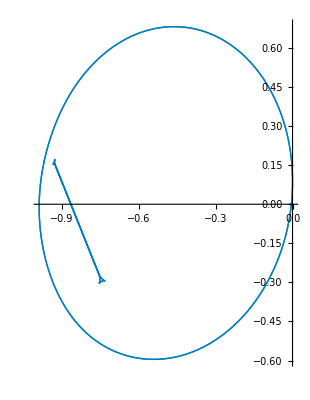

```mathematica
plv3grouprot=ParametricPlot[{{v3grouprotorthotoplot[[1]][[2]],v3grouprotorthotoplot[[1]][[4]]},{v3grouprotorthotoplot[[2]][[2]],v3grouprotorthotoplot[[2]][[4]]},{v3grouprotorthotoplot[[3]][[2]],v3grouprotorthotoplot[[3]][[4]]},{v3grouprotorthotoplot[[4]][[2]],v3grouprotorthotoplot[[4]][[4]]}},{alpha,0,2*Pi},PlotStyle->{RGBColor[0,.5,.75]},PlotPoints->100]
```

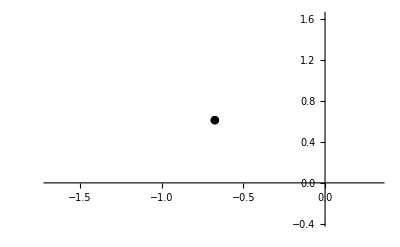

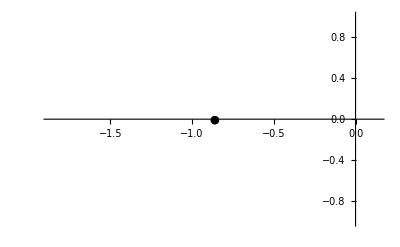

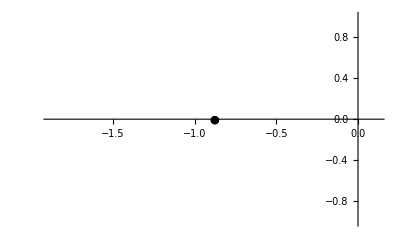

```mathematica
figfluidvelortho=ListPlot[{{v3uortho[[2]],v3uortho[[4]]}},PlotStyle->Black,PlotMarkers->{Automatic,Medium}]
figfluidvelrotortho=ListPlot[{{v3urotortho[[2]],v3urotortho[[4]]}},PlotStyle->Black,PlotMarkers->{Automatic,Medium}]
figcms=ListPlot[{{-Sqrt[cms2],0}},PlotStyle->Black,PlotMarkers->{Automatic,Medium}]
```

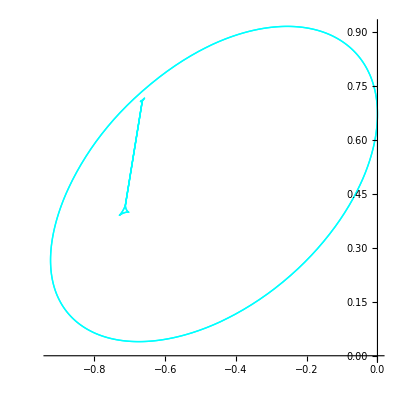

```mathematica
(* r-phi plane for the full quartic solution *)
plv3group=ParametricPlot[{{v3grouporthotoplot[[1]][[2]],v3grouporthotoplot[[1]][[4]]},{v3grouporthotoplot[[2]][[2]],v3grouporthotoplot[[2]][[4]]},{v3grouporthotoplot[[3]][[2]],v3grouporthotoplot[[3]][[4]]},{v3grouporthotoplot[[4]][[2]],v3grouporthotoplot[[4]][[4]]}},{alpha,0,2*Pi},PlotStyle->{RGBColor[0,1,1]},PlotPoints->100]
```

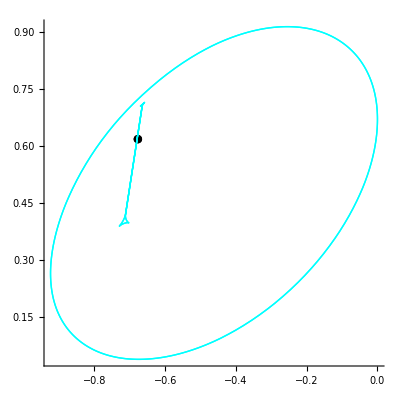

figboosted.eps

```mathematica
figboosted1=Show[figfluidvelortho,plv3group,AspectRatio->1]
Export["figboosted.eps",figboosted1]
```

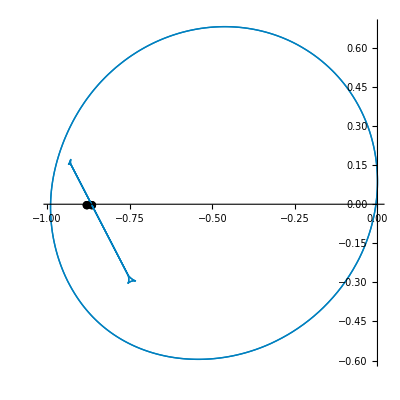

figboosted.eps

```mathematica
figboosted2=Show[figfluidvelrotortho,plv3grouprot,figcms,AspectRatio->1]
Export["figboosted.eps",figboosted2]
```

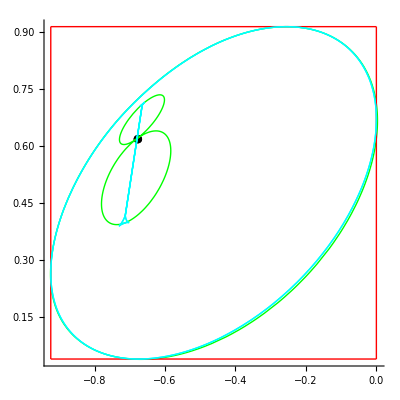

figzoom1.eps

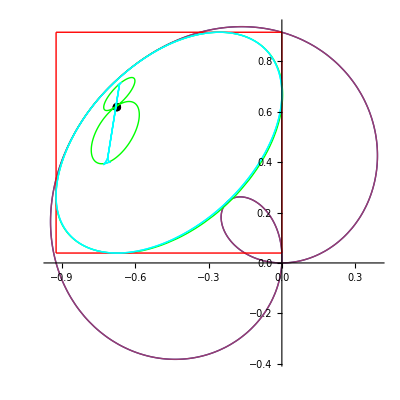

fig1.eps

```mathematica
figzoom=Show[figfluidvelortho,plboostu,plotvpm,plv3group,AspectRatio->1]
Export["figzoom1.eps",figzoom]
fig=Show[figfluidvelortho,plboostk,plboostu,plotvpm,plv3group,AspectRatio->1]
Export["fig1.eps",fig]
```

```mathematica
(* Done *)
```